# 3基盤ログの解析:推定ユーザーごとのアクセス推移（ユーザーストーリー）

-Graphics-

生ログ

## 準備

```mathematica
start=AbsoluteTime[Date[]]
```

3.908880701024752×10^9

#### 変数

```mathematica
date="20230724-20230725-ipaddr"
```

20230724-20230725-ipaddr

```mathematica
case={"ci","cs","la","wk"}
```

{ci,cs,la,wk}

```mathematica
base["ci"]="T=ci.P~5"
base["cs"]="T=cs.R=.P="
base["la"]="T=la.T~ea.A~hc.A~go.A~bot.P~api"
base["wk"]="T=wk.P~4.A~bot"
base["all"]="T=4"
```

T=ci.P~5

T=cs.R=.P=

T=la.T~ea.A~hc.A~go.A~bot.P~api

T=wk.P~4.A~bot

T=4

```mathematica
mountdir="/Volumes/IODATA/NII/togo-log/rcoslogs/"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/

#### 解析用データ

```mathematica
fileliststr=Import[mountdir<>"log/D="<>date<>"/"<>"filenames","String"]
```

log-20230724-20230725_ipaddr.rcoslog003.log

```mathematica
filelist=StringSplit[fileliststr]
```

{log-20230724-20230725_ipaddr.rcoslog003.log}

元ログの大きさ （wc）

```mathematica
logwc=Import[mountdir<>"log/D="<>date<>"/logfiles.wc","String"]
```

1205   18078  595028 log-20230724-20230725_ipaddr.rcoslog003.log

```mathematica
ckanfile=mountdir<>"crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/crid/CIRDEV-1067_crid_list/ckan_product_crid_list.txt

```mathematica
ckanSt=Import[ckanfile,"String"];
```

```mathematica
(ckanName=StringSplit[ckanSt,"\n"])//Dimensions
```

{92643}

```mathematica
(ckanCridAC=Apply[Association,Map[#->#&,ckanName]])//Dimensions
```

{92643}

#### プログラム

vertexを指定してdirected-edgeを辿る部分グラフ抽出の関数：

```mathematica
directedConnectedGraphComponent[g_,v_]:=Module[{vAll,vOther,addEdge},
vAll=VertexList[g];
vOther=Complement[vAll,{v}];
addEdge=Map[#->v&,vOther];
Subgraph[g,ConnectedComponents[Flatten[{EdgeList[g],addEdge},1],v][[1]]]
]
```

グラフよりinがないノードを検出してそこから(g,v)に対して上記関数をアプライする関数：

```mathematica
vertexInGraph[g_Graph]:=Module[{deg,pos,vname},
deg=VertexInDegree[g];
pos=Position[deg,0]//Flatten//Union;
vname=VertexList[g][[pos]];
Map[directedConnectedGraphComponent[g,#]&,vname]
]
vertexInGraph[g_Integer]:=g
```

story-group-indexを各グラフにdistributeする関数：

```mathematica
distributeIdxGr[idxGr_]:=Module[
{date,idx,gr},
date=idxGr[[1]];
idx=idxGr[[2]];
gr=idxGr[[3]];
Map[{date,idx,#}&,gr]
]
```

stringからfqdnのみ抽出する関数：

```mathematica
fqdnFromPath[s_]:=StringJoin[StringSplit[s,"/"]⟦{1,3}⟧]
```

```mathematica
fqdnFromGraph[g_Graph]:=Union[Sort[Map[fqdnFromPath,VertexList[g]]]]
```

## リンク(4)

### データ(ci)

```mathematica
dir["ci"]=mountdir<>"log/D="<>date<>"/"<>base["ci"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=ci.P~5

#### データの読み込み

```mathematica
file["ci"]="self.1"
```

self.1

```mathematica
str["ci"]=Import[dir["ci"]<>"/"<>file["ci"],"String"];
```

```mathematica
(strSplt["ci"]=StringSplit[str["ci"],"\n"])//Length
```

34

```mathematica
(strSplt1["ci"]=Map[StringSplit[#,"\t"]&,strSplt["ci"]])//Dimensions
```

{34,15}

#### カラムポジションの調整

不要。

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1C["ci"]=Map[ReplacePart[#,8->"https://cir.nii.ac.jp/"<>StringDrop[#[[8]],8]]&,strSplt1["ci"]];
```

レファラーのキーを削除する。

```mathematica
strSplt1CC["ci"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["ci"]];
```

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["ci"][s_String]:=AbsoluteTime[DateList[StringTake[s,{8,-6}]]]
```

```mathematica
logdateToTime["ci"][strSplt1CC["ci"][[1]][[6]]]
```

3.8992×10^9

```mathematica
strSplt1CCC["ci"]=Map[ReplacePart[#,6->logdateToTime["ci"][#[[6]]]]&,strSplt1CC["ci"]];
```

remoteをアドレスのみに。

```mathematica
ip["ci"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCCpre["ci"]=Map[ReplacePart[#,3->ip["ci"][#[[3]]]]&,strSplt1CCC["ci"]];
```

```mathematica
strSplt1CCCCpre["ci"][[10]]//TableForm
```

2023-07-24T23:41:32Z
log.ci0001.aws.wa04.yobi
136.187.176.53
host":"-
user":"-
3.89926×10^9
method":"GET
https://cir.nii.ac.jp/all
code":"200
size":"10509
-
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/114.0.0.0 Safari/537.36
http_x_forwarded_for":"\"136.187.176.53\"
request_time":"0.012
upstream_response_time":"0.012"}

pathのCRID、refererのCRIDを追加。

```mathematica
toCRID[s_String/;StringMatchQ[s,RegularExpression["https://cir.nii.ac.jp/crid/.*"]]]:=StringTake[StringSplit[s,"/"][[5]],19]
```

```mathematica
strSplt1CCCC["ci"]=Map[Join[#,{toCRID[#[[8]]],toCRID[#[[11]]]}]&,strSplt1CCCCpre["ci"]];
```

```mathematica
strSplt1CCCC["ci"][[8]]//TableForm
```

2023-07-24T23:41:23Z
log.ci0001.aws.wa04.yobi
136.187.176.53
host":"-
user":"-
3.89926×10^9
method":"GET
https://cir.nii.ac.jp/all?q=A%20OR%20NOT%20A&dataSourceType=PUBLIC_DATA
code":"200
size":"17845
-
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/114.0.0.0 Safari/537.36
http_x_forwarded_for":"\"136.187.176.53\"
request_time":"0.035
upstream_response_time":"0.035"}
toCRID[https://cir.nii.ac.jp/all?q=A%20OR%20NOT%20A&dataSourceType=PUBLIC_DATA]
toCRID[-]

### データ(cs)

```mathematica
dir["cs"]=mountdir<>"log/D="<>date<>"/"<>base["cs"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=cs.R=.P=

#### データの読み込み

```mathematica
file["cs"]="self.1"
```

self.1

```mathematica
str["cs"]=Import[dir["cs"]<>"/"<>file["cs"],"String"];
```

```mathematica
(strSplt["cs"]=StringSplit[str["cs"],"\n"])//Length
```

118

```mathematica
(strSplt1["cs"]=Map[StringSplit[#,"\t"]&,strSplt["cs"]])//Dimensions
```

{118,14}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 5
4: <- 4
5: <- 6
6: date <- 3
7: <- 7
8: path <- 9
9: <- 8
10: <- 10
11: ref <- 12
12: agent <- 13
13: <- 11
14: <- 14

```mathematica
rp["cs"]={1,2,5,4,6,3,7,9,8,10,12,13,11,14}
```

{1,2,5,4,6,3,7,9,8,10,12,13,11,14}

```mathematica
(strSplt1R["cs"]=Map[#[[rp["cs"]]]&,strSplt1["cs"]])//Dimensions
```

{118,14}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
strSplt1R["cs"][[1]][[8]]
```

path":"/

```mathematica
pathhead["cs"]="https://jupyter.cs.rcos.nii.ac.jp"
```

https://jupyter.cs.rcos.nii.ac.jp

```mathematica
pathreplace["cs"][path_]:=Module[{pathhead,epath},
pathhead="https://jupyter.cs.rcos.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["cs"]=Map[ReplacePart[#,8->pathreplace["cs"][#[[8]]]]&,strSplt1R["cs"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["cs"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["cs"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["cs"][s_String]:=AbsoluteTime[DateList[StringTake[s,{16,-7}]]]
```

```mathematica
strSplt1CC["cs"][[1]][[6]]
```

{"time_local":"2023-07-25T16:04:31.556381164+09:00

```mathematica
strSplt1CCC["cs"]=Map[ReplacePart[#,6->logdateToTime["cs"][#[[6]]]]&,strSplt1CC["cs"]];
```

remoteをアドレスのみに。

```mathematica
ip["cs"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["cs"]=Map[ReplacePart[#,3->ip["cs"][#[[3]]]]&,strSplt1CCC["cs"]];
```

```mathematica
strSplt1CCCC["cs"][[10]]//TableForm
```

2023-07-25T07:04:56Z
log.cs0002.ksw.wa01.yobi
136.187.176.53
stream":"stdout
user":"-
3.89929×10^9
date_time":"25/Jul/2023:07:04:55 +0000
https://jupyter.cs.rcos.nii.ac.jp/hub/static/css/style.min.css?v=b765bd061cb3c09b380c86c0958879542c33c0a69df364b9cbd772ddfb93cec5c9687d3b3ed64d8232de6395f1cf651cffff7e113ecb016fa5ac124bdc78ad5c
method":"GET
code":"200
https://jupyter.cs.rcos.nii.ac.jp/hub/home
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/114.0.0.0 Safari/537.36
size":"154594
hostname":"fluentd-bllnp"}

### データ(la)

```mathematica
dir["la"]=mountdir<>"log/D="<>date<>"/"<>base["la"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=la.T~ea.A~hc.A~go.A~bot.P~api

laのログに関し23・9中頃よりsession_idが入る。(12 カラム目 -> 10 カラム目)

#### データの読み込み

```mathematica
file["la"]="self.1"
```

self.1

```mathematica
str["la","pre"]=Import[dir["la"]<>"/"<>file["la"],"String"];
```

```mathematica
(strSplt["la","pre"]=StringSplit[str["la","pre"],"\n"])//Length
```

0

```mathematica
(strSplt1["la","pre"]=Map[StringSplit[#,"\t"]&,strSplt["la","pre"]])//Dimensions
```

{0}

```mathematica
Map[#[[2]]&,strSplt1["la","pre"]]//Tally
```

{}

"log.la0001.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0001.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0001.aws.wa01.yobi"&])//Dimensions
```

{0}

"log.la0002.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0002.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0002.aws.wa01.yobi"&])//Dimensions
```

{0}

"log.la0003.aws.wa01.yobi" の分離

```mathematica
(strSplt1["la","log.la0003.aws.wa01.yobi"]=Select[strSplt1["la","pre"],#[[2]]=="log.la0003.aws.wa01.yobi"&])//Dimensions
```

{0}

#### カラムポジションの調整

"log.la0001.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0001.aws.wa01.yobi"][[1]]//TableForm
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0001.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0001.aws.wa01.yobi"]=Map[#[[rp["la","log.la0001.aws.wa01.yobi"]]]&,strSplt1["la","log.la0001.aws.wa01.yobi"]])//Dimensions
```

{0}

"log.la0002.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0002.aws.wa01.yobi"][[1]]//TableForm
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0002.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0002.aws.wa01.yobi"]=Map[#[[rp["la","log.la0002.aws.wa01.yobi"]]]&,strSplt1["la","log.la0002.aws.wa01.yobi"]])//Dimensions
```

{0}

"log.la0003.aws.wa01.yobi"

```mathematica
strSplt1["la","log.la0003.aws.wa01.yobi"][[1]]//TableForm
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: http_x_forwarded_for (remote) <- 11 
4: <- 8
5: <- 5
6: date <- 4
7: <- 7
8: path <- 6
9: <- 3
10: <- 12
11: ref <- 9
12: agent <- 10

```mathematica
rp["la","log.la0003.aws.wa01.yobi"]={1,2,11,8,5,4,7,6,3,12,9,10}
```

{1,2,11,8,5,4,7,6,3,12,9,10}

```mathematica
(strSplt1R["la","log.la0003.aws.wa01.yobi"]=Map[#[[rp["la","log.la0003.aws.wa01.yobi"]]]&,strSplt1["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{0}

3サービスをマージ

```mathematica
(strSplt1R["la"]=Join[strSplt1R["la","log.la0001.aws.wa01.yobi"],strSplt1R["la","log.la0002.aws.wa01.yobi"],strSplt1R["la","log.la0003.aws.wa01.yobi"]])//Dimensions
```

{0}

```mathematica
strSplt1R["la"][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["la"]="https://lms.nii.ac.jp"
```

https://lms.nii.ac.jp

```mathematica
pathreplace["la"][path_]:=Module[{pathhead,epath},
pathhead="https://lms.nii.ac.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["la"]=Map[ReplacePart[#,8->pathreplace["la"][#[[8]]]]&,strSplt1R["la"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["la"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["la"]];
```

時刻をMathematica標準にする。

```mathematica
logdateToTime["la"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
StringTake[strSplt1CC["la"][[1]][[6]],{13,-6}]//DateList//AbsoluteTime
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 6 of {}⟦1⟧ does not exist.

StringTake::strse: String or list of strings expected at position 1 in StringTake[{}⟦1⟧⟦6⟧,{13,-6}].

DateList::arg: Argument StringTake[{}⟦1⟧⟦6⟧,{13,-6}] cannot be interpreted as a date or time input.

AbsoluteTime::arg: Argument DateList[StringTake[{}⟦1⟧⟦6⟧,{13,-6}]] cannot be interpreted as a date or time input.

AbsoluteTime[DateList[StringTake[{}⟦1⟧⟦6⟧,{13,-6}]]]

```mathematica
strSplt1CCC["la"]=Map[ReplacePart[#,6->logdateToTime["la"][#[[6]]]]&,strSplt1CC["la"]];
```

```mathematica
strSplt1CCC["la"][[1]]//TableForm
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

http_x_forwarded_for (remote)をアドレスのみに。

```mathematica
ip["la"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
(strSplt1CCCC["la"]=Map[ReplacePart[#,3->ip["la"][#[[3]]]]&,strSplt1CCC["la"]])//Dimensions
```

{0}

```mathematica
strSplt1CCCC["la"][[1]]//TableForm
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

### データ(wk)

```mathematica
dir["wk"]=mountdir<>"log/D="<>date<>"/"<>base["wk"]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=wk.P~4.A~bot

#### データの読み込み

```mathematica
file["wk"]="self.1"
```

self.1

```mathematica
str["wk"]=Import[dir["wk"]<>"/"<>file["wk"],"String"];
```

```mathematica
(strSplt["wk"]=StringSplit[str["wk"],"\n"])//Length
```

107

```mathematica
(strSplt1["wk"]=Map[StringSplit[#,"\t"]&,strSplt["wk"]])//Dimensions
```

{107,12}

#### カラムポジションの調整

CiRとカラムポジションをあわせる
1: <- 1
2: <- 2
3: remote <- 3
4: <- 4
5: <- 6
6: date <- 5
7: <- 8
8: path <- 7
9: <- 9
10: <- 12
11: ref <- 10
12: agent <- 11

```mathematica
rp["wk"]={1,2,3,4,6,5,8,7,9,12,10,11}
```

{1,2,3,4,6,5,8,7,9,12,10,11}

```mathematica
(strSplt1R["wk"]=Map[#[[rp["wk"]]]&,strSplt1["wk"]])//Dimensions
```

{107,12}

#### 各値の補完

パスのキーを削除しURLを補完する。

```mathematica
pathhead["wk"]="https://jdcat.jsps.go.jp"
```

https://jdcat.jsps.go.jp

```mathematica
pathreplace["wk"][path_]:=Module[{pathhead,epath},
pathhead="https://jdcat.jsps.go.jp";
epath=StringDrop[path,7];
If[StringTake[epath,1]=="/",pathhead<>epath,epath]
]
```

```mathematica
strSplt1C["wk"]=Map[ReplacePart[#,8->pathreplace["wk"][#[[8]]]]&,strSplt1R["wk"]];
```

レファラーのキーを削除する。(11カラム目でないといけない)

```mathematica
strSplt1CC["wk"]=Map[ReplacePart[#,11->StringDrop[#[[11]],10]]&,strSplt1C["wk"]];
```

レファラーになにも入っていない。設定されていないのではなく入ってきていないだけであることを確認済み。

時刻をMathematica標準にする。

ログのdateをWLの時間表現に変換する関数

```mathematica
logdateToTime["wk"][s_String]:=AbsoluteTime[DateList[StringTake[s,{13,-6}]]]+(9*60*60)
```

```mathematica
strSplt1CC["wk"][[1]][[6]]
```

date_time":"2023-07-25T05:19:33+0000

```mathematica
strSplt1CC["wk"][[1]][[6]]//logdateToTime["wk"]
```

3.89928×10^9

```mathematica
strSplt1CCC["wk"]=Map[ReplacePart[#,6->logdateToTime["wk"][#[[6]]]]&,strSplt1CC["wk"]];
```

remoteをアドレスのみに。

```mathematica
ip["wk"][str_]:=StringSplit[str,"\":\""][[2]]
```

```mathematica
strSplt1CCCC["wk"]=Map[ReplacePart[#,3->ip["wk"][#[[3]]]]&,strSplt1CCC["wk"]];
```

```mathematica
strSplt1CCCC["wk"][[26]]//TableForm
```

2023-07-25T06:41:51Z
log.wk1001.oci.wa01.yobi
136.187.176.53
user":"-
method":"GET
3.89929×10^9
code":"200
https://jdcat.jsps.go.jp/
size":"11384
http_x_forwarded_for":"136.187.176.53"}
https://jdcat.jsps.go.jp/signup/
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/114.0.0.0 Safari/537.36

### データの合成

ソートも行う。

ソートキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

```mathematica
Timing[(strSplt1CCCC[3]=SortBy[Join[strSplt1CCCC["ci"],strSplt1CCCC["cs"],strSplt1CCCC["wk"]],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{0.001543,{259}}

抽出ログの行インデックスをアペンド:

```mathematica
apIdx[3]=Table[i,{i,Length[strSplt1CCCC[3]]}];
```

```mathematica
(idxLog[3]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC[3],apIdx[3]}]])//Dimensions
```

{259}

### ckanデータの処理(基盤全て)

CKAN-CRIDの存在確認とハッシュの生成：

パスのハッシュ：

```mathematica
(ckanPathE[3]=Map[ckanCridAC[#[[-3]]]&,idxLog[3]])//Dimensions
```

{259}

```mathematica
(ckanCridPLogPos[3]=Flatten[Position[ckanPathE[3],_String,{1}]])//Length
```

0

```mathematica
(ckanCridPLogPosAC[3]=Association[Map[#->#&,ckanCridPLogPos[3]]])//Length
```

0

リファラーのハッシュ：

```mathematica
(ckanRefE[3]=Map[ckanCridAC[#[[-2]]]&,idxLog[3]])//Dimensions
```

{259}

```mathematica
(ckanCridRLogPos[3]=Flatten[Position[ckanRefE[3],_String,{1}]])//Length
```

0

```mathematica
(ckanCridRLogPosAC[3]=Association[Map[#->#&,ckanCridRLogPos[3]]])//Length
```

0

パス or リファラーのハッシュ：

```mathematica
(ckanCridPRLogPos[3]=Union[ckanCridPLogPos[3],ckanCridRLogPos[3]])//Length
```

0

```mathematica
(ckanCridPRLogPosAC[3]=Association[Map[#->#&,ckanCridPRLogPos[3]]])//Length
```

0

## リンク(ci)

```mathematica
Timing[(strSplt1CCCC["ci"]=SortBy[strSplt1CCCC["ci"],{#[[3]],#[[12]],#[[6]]}&])//Dimensions]
```

{0.000199,{34,17}}

抽出ログの行インデックスをアペンド

```mathematica
apIdx["ci"]=Table[i,{i,Length[strSplt1CCCC["ci"]]}];
```

```mathematica
idxLog["ci"]=Map[Append[#[[1]],#[[2]]]&,Transpose[{strSplt1CCCC["ci"],apIdx["ci"]}]];
```

```mathematica
idxLog["ci"][[1]]//TableForm
```

2023-07-24T23:40:19Z
log.ci0001.aws.wa04.yobi
136.187.176.53
host":"-
user":"-
3.89926×10^9
method":"GET
https://cir.nii.ac.jp/all?q=A%20OR%20NOT%20A&dataSourceType=PUBLIC_DATA
code":"200
size":"17845
-
agent":"Mozilla/5.0 (Macintosh; Intel Mac OS X 10_15_7) AppleWebKit/537.36 (KHTML, like Gecko) Chrome/114.0.0.0 Safari/537.36
http_x_forwarded_for":"\"136.187.176.53\"
request_time":"2.788
upstream_response_time":"2.788"}
toCRID[https://cir.nii.ac.jp/all?q=A%20OR%20NOT%20A&dataSourceType=PUBLIC_DATA]
toCRID[-]
1

### ckanデータの処理(ciのみ)

CKAN-CRIDの存在確認：

```mathematica
(ckanPathE["ci"]=Map[ckanCridAC[#[[-3]]]&,idxLog["ci"]])//Dimensions
```

{34}

```mathematica
ckanCridPlist=Cases[ckanPathE["ci"],_String]
```

{}

```mathematica
ckanRefE=.
```

```mathematica
ckanRefE["ci"]=Map[ckanCridAC[#[[-2]]]&,idxLog["ci"]];
```

```mathematica
ckanCridRlist=Cases[ckanRefE["ci"],_String]
```

{}

```mathematica
ckanCridPRU=Union[ckanCridPlist,ckanCridRlist]
```

{}

```mathematica
ckanCridPRACQ=Association[Map[#->True&,ckanCridPRU]]
```

<||>

## ユーザー生成(4)

各条件のキーを策定：

3項のソースアドレス

12項のユーザーエージェント

6項のアクセス時刻

まず推定ユーザーごとにgathgerする。

#### ユーザー生成

ソースアドレスとユーザーエージェントをキーにしてsplitする。

```mathematica
(idxLogS[3]=Split[idxLog[3],#1[[3]]==#2[[3]]&&#1[[12]]==#2[[12]]&])//Length
```

2

上記の数が推定ユーザー数。

## グラフ生成(4):inf

#### Pre Op 1

ストーリー分割：

時間設定をinfにすることによりアクセス時間では分割しない。
1. ユーザーごとに分割 -> userGr,userGrIdx
2. 繋がらないエッジで分割 -> user2GrIdx
3. 上記の各グラフより in がないVertexを起点としてoutで辿れるパスにより各サブグラフを抽出 -> storyGrIdx
　のちに扱いやすい構造にする。

0. 時間で分割しない -> 全てを要素1のリストにする：

```mathematica
Timing[(idxLogSinf[3]=Map[Split[#,#2[[6]]-#1[[6]]<=Infinity&]&,idxLogS[3]])//Dimensions]
```

{0.000677,{2,1}}

ユーザーストーリーグループに対応するログを参照する関数：

```mathematica
refstglog[3][g_]:={g[[1]],g[[3]],Part[idxLogSinf[3],g[[2,1]],g[[2,2]]]}
```

#### Pre Op 2.1

Saveデータがある時は読み込む：

```mathematica
SetDirectory["/Volumes/elecom/NII/togo-log/rcoslogs/log/D="<>date<>"/"<>base["all"]<>"/_story"]
```

SetDirectory::cdir: Cannot set current directory to /Volumes/elecom/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=4/_story.

$Failed

```mathematica
Timing[Get["storyGrIdxFlDs.save"];]
```

Get::noopen: Cannot open storyGrIdxFlDs.save.

{0.009903,Null}

#### Pre Op 2.2

<<< Saveデータを読んだ時はここから飛ばす。 >>>

1. ユーザーごとのグラフ生成：

エッジルール作成（この時点でエッジ以外の情報が落ちる、アクセス時刻とログ行インデックスをエッジに設定する）：

```mathematica
userGrER[3]=Map[Map[DirectedEdge[#[[11]],#[[8]],{#[[6]],#[[-1]]}]&,#]&,idxLogSinf[3],{2}];
```

```mathematica
userGrER[3][[2]]
```

{{-https://cir.nii.ac.jp/all?q=%E6%97%A5%E6%9C%AC%E6%95%99%E5%B8%AB%E5%AD%A6%E4%BC%9Ahttps://cir.nii.ac.jp/all?q=%E6%95%99%E5%B8%AB%E5%AD%A6{3.8992×10^9,259}}}

```mathematica
(userGr[3]=Map[Graph[#,VertexLabels->Automatic]&,userGrER[3],{2}])//Length
```

2

上記がユーザー数。

ここでindexを作成。{date,{userID, log-groupID}, G} とする。

```mathematica
userGrIdx[3]=MapIndexed[{date,#2,#1}&,userGr[3],{2}];
```

2. ユーザーごとのグラフをさらにエッジでつながらない部分グラフに分ける：

```mathematica
Timing[(user2GrIdx[3]=Map[{#[[1]],#[[2]],WeaklyConnectedGraphComponents[#[[3]]]}&,userGrIdx[3],{2}])//Dimensions] (**)
```

{0.008153,{2,1,3}}

3. 分けられた各グラフをさらにinがないノードをスタートとするグラフに分ける：

```mathematica
Timing[(storyGrIdx[3]=Map[vertexInGraph,user2GrIdx[3],{4}])//Dimensions ]
```

{0.021921,{2,1,3}}

扱いやすい構造にする。-> storyGrIdxFlDs[4]

グラフリストをflatten:

```mathematica
(storyGrIdxFl[3]=Map[{#[[1]],#[[2]],Flatten[#[[3]]]}&,Flatten[storyGrIdx[3],1]])//Dimensions
```

{2,3}

```mathematica
storyGrIdxFl[3][[1]][[3]][[1]]//EdgeList
```

{https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/get_path_name_dict/1613031614318?time=1690262373912{3.89928×10^9,15},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/get_path_name_dict/1613031614318?time=1690267312251{3.89929×10^9,55},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/get_path_name_dict/1613031614318?time=1690267922878{3.89929×10^9,67},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/{3.89929×10^9,68},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/get_path_name_dict/1613031614318?time=1690267932531{3.89929×10^9,73},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/records/27367{3.89929×10^9,75},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/records/9341{3.89929×10^9,83},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/get_path_name_dict/1613031614318?time=1690269443778{3.89929×10^9,160},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/search?page=1&size=20&sort=wtl&Distributor=SSJ%20%E3%83%87%E3%83%BC%E3%82%BF%E3%82%A2%E3%83%BC%E3%82%AB%E3%82%A4%E3%83%96&is_facet_search=true{3.89929×10^9,161},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/get_path_name_dict/1613031614318?time=1690269593883{3.89929×10^9,181},https://jdcat.jsps.go.jp/?page=1&size=20&sort=wtlhttps://jdcat.jsps.go.jp/get_path_name_dict/1613031614318?time=1690269775737{3.89929×10^9,196},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_child_list/1613031614318?time=1690262373912{3.89928×10^9,11},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89928×10^9,12},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,52},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,63},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,70},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,157},https://jdcat.jsps.go.jp/search?page=1&size=20&sort=wtl&Distributor=SSJ%20%E3%83%87%E3%83%BC%E3%82%BF%E3%82%A2%E3%83%BC%E3%82%AB%E3%82%A4%E3%83%96&is_facet_search=truehttps://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,162},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,177},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,182},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,193},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,197},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/journal_info/1613031614318{3.89928×10^9,13},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/journal_info/1613031614318{3.89929×10^9,53},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/journal_info/1613031614318{3.89929×10^9,64},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/journal_info/1613031614318{3.89929×10^9,71},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/journal_info/1613031614318{3.89929×10^9,158},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/journal_info/1613031614318{3.89929×10^9,178},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/journal_info/1613031614318{3.89929×10^9,194},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89928×10^9,14},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,54},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,65},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,72},https://jdcat.jsps.go.jp/records/27367https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,76},https://jdcat.jsps.go.jp/records/9341https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,84},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,159},https://jdcat.jsps.go.jp/search?page=1&size=20&sort=wtl&Distributor=SSJ%20%E3%83%87%E3%83%BC%E3%82%BF%E3%82%A2%E3%83%BC%E3%82%AB%E3%82%A4%E3%83%96&is_facet_search=truehttps://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,163},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,179},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,195},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_child_list/1613031614318?time=1690267312251{3.89929×10^9,51},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_child_list/1613031614318?time=1690267922878{3.89929×10^9,62},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_child_list/1613031614318?time=1690267932531{3.89929×10^9,69},https://jdcat.jsps.go.jp/https://jupyter.cs.rcos.nii.ac.jp/{3.89929×10^9,86},https://jdcat.jsps.go.jp/https://jupyter.cs.rcos.nii.ac.jp/{3.89929×10^9,107},https://jdcat.jsps.go.jp/https://jupyter.cs.rcos.nii.ac.jp/{3.89929×10^9,126},https://jdcat.jsps.go.jp/https://jupyter.cs.rcos.nii.ac.jp/hub/{3.89929×10^9,127},https://jdcat.jsps.go.jp/https://jupyter.cs.rcos.nii.ac.jp/hub/home{3.89929×10^9,128},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_child_list/1613031614318?time=1690269443778{3.89929×10^9,156},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_child_list/1613031614318?time=1690269593883{3.89929×10^9,180},https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,184},https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,187},https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20https://jdcat.jsps.go.jp/facet-search/get-title-and-order{3.89929×10^9,199},https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20https://jdcat.jsps.go.jp/get_search_setting{3.89929×10^9,200},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20{3.89929×10^9,183},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20{3.89929×10^9,198},https://jdcat.jsps.go.jp/https://jdcat.jsps.go.jp/get_child_list/1613031614318?time=1690269775737{3.89929×10^9,192},https://jdcat.jsps.go.jp/https://jupyter.cs.rcos.nii.ac.jp/v2/weko3/https%3A%2F%2Fjdcat.jsps.go.jp%2Frecords%2F13727/1898bef400a166{3.89929×10^9,205},https://jdcat.jsps.go.jp/https://jupyter.cs.rcos.nii.ac.jp/v2/weko3/https%3A%2F%2Fjdcat.jsps.go.jp%2Frecords%2F13727/1898bef400a166{3.89929×10^9,207},https://jdcat.jsps.go.jp/https://jupyter.cs.rcos.nii.ac.jp/oauth_callback?code=H1VJnNBhQWf2BziuAqxjQOU5Wsou8A&state=eyJ1dWlkIjogImJmYjVlMWM3ZGIyODRjYTBhODA0ZGM0ZjUxYTU3MWRiIiwgIm5leHRfdXJsIjogIi92Mi93ZWtvMy9odHRwcyUzQSUyRiUyRmpkY2F0LmpzcHMuZ28uanAlMkZyZWNvcmRzJTJGMTM3MjcvMTg5OGJlZjQwMGExNjYifQ{3.89929×10^9,206},https://jdcat.jsps.go.jp/records/9341https://jdcat.jsps.go.jp/analysis.html{3.89929×10^9,85},https://jupyter.cs.rcos.nii.ac.jp/https://jupyter.cs.rcos.nii.ac.jp/favicon.ico{3.89929×10^9,87},https://jupyter.cs.rcos.nii.ac.jp/https://jupyter.cs.rcos.nii.ac.jp/favicon.ico{3.89929×10^9,108},https://jupyter.cs.rcos.nii.ac.jp/https://jupyter.cs.rcos.nii.ac.jp/Shibboleth.sso/DS?SAMLDS=1&target=ss%3Amem%3A26ae9f8a5ceac8ee627e11c8fedde97e1550526d9f06f4774be5efb411aacae9&entityID=https%3A%2F%2Fidp.nii.ac.jp%2Fidp%2Fshibboleth{3.89929×10^9,88},https://jupyter.cs.rcos.nii.ac.jp/https://jupyter.cs.rcos.nii.ac.jp/Shibboleth.sso/DS?SAMLDS=1&target=ss%3Amem%3Ab5638fba2ecfa8e5b6f273b6ec662ce8fce1c9b14a682ee0b129f475a03ec3a3&entityID=https%3A%2F%2Fidp.nii.ac.jp%2Fidp%2Fshibboleth{3.89929×10^9,109},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/css/style.min.css?v=b765bd061cb3c09b380c86c0958879542c33c0a69df364b9cbd772ddfb93cec5c9687d3b3ed64d8232de6395f1cf651cffff7e113ecb016fa5ac124bdc78ad5c{3.89929×10^9,95},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/css/style.min.css?v=b765bd061cb3c09b380c86c0958879542c33c0a69df364b9cbd772ddfb93cec5c9687d3b3ed64d8232de6395f1cf651cffff7e113ecb016fa5ac124bdc78ad5c{3.89929×10^9,116},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/requirejs/require.js?v=bd1aa102bdb0b27fbf712b32cfcd29b016c272acf3d864ee8469376eaddd032cadcf827ff17c05a8c8e20061418fe58cf79947049f5c0dff3b4f73fcc8cad8ec{3.89929×10^9,96},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/requirejs/require.js?v=bd1aa102bdb0b27fbf712b32cfcd29b016c272acf3d864ee8469376eaddd032cadcf827ff17c05a8c8e20061418fe58cf79947049f5c0dff3b4f73fcc8cad8ec{3.89929×10^9,119},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/jquery/dist/jquery.min.js?v=de027062931edd07b01842eff24fc15fdbdcaa1af245dcd133155faba9e0c965f0a34dc6144ce3b149bc43b4597073c792cb6dabbfc6168c63095523923bcf77{3.89929×10^9,97},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/jquery/dist/jquery.min.js?v=de027062931edd07b01842eff24fc15fdbdcaa1af245dcd133155faba9e0c965f0a34dc6144ce3b149bc43b4597073c792cb6dabbfc6168c63095523923bcf77{3.89929×10^9,118},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/logo{3.89929×10^9,98},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/logo{3.89929×10^9,120},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/js/home.js?v=20230724080715{3.89929×10^9,99},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/js/home.js?v=20230724080715{3.89929×10^9,121},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/moment/moment.js?v=20230724080715{3.89929×10^9,101},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/moment/moment.js?v=20230724080715{3.89929×10^9,123},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/js/utils.js?v=20230724080715{3.89929×10^9,102},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/js/utils.js?v=20230724080715{3.89929×10^9,125},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/bootstrap/dist/js/bootstrap.min.js?v=a014e9acc78d10a0a7a9fbaa29deac6ef17398542d9574b77b40bf446155d210fa43384757e3837da41b025998ebfab4b9b6f094033f9c226392b800df068bce{3.89929×10^9,117},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/static/favicon.ico?v=fde5757cd3892b979919d3b1faa88a410f28829feb5ba22b6cf069f2c6c98675fceef90f932e49b510e74d65c681d5846b943e7f7cc1b41867422f0481085c1f{3.89929×10^9,124},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/spawn/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh{3.89929×10^9,129},https://jupyter.cs.rcos.nii.ac.jp/hub/spawn-pending/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xhhttps://jupyter.cs.rcos.nii.ac.jp/hub/spawn-pending/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh{3.89929×10^9,131},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/hub/spawn-pending/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh{3.89929×10^9,130},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz{3.89929×10^9,243},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?{3.89929×10^9,250},https://jupyter.cs.rcos.nii.ac.jp/hub/homehttps://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?{3.89929×10^9,244},https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20https://jdcat.jsps.go.jp/get_child_list/%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF?time=1690269609294{3.89929×10^9,185},https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20https://jdcat.jsps.go.jp/journal_info/%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF{3.89929×10^9,186},https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20https://jdcat.jsps.go.jp/journal_info/%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF{3.89929×10^9,202},https://jdcat.jsps.go.jp/search?page=1&search_type=0&q=%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF&sort=wtl&size=20https://jdcat.jsps.go.jp/get_child_list/%E8%B3%87%E6%9C%AC%E3%83%BB%E6%8A%95%E8%B3%87%E3%83%87%E3%83%BC%E3%82%BF?time=1690269796094{3.89929×10^9,201},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/custom/custom.css{3.89929×10^9,245},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/custom/custom.js?v=20230725073105{3.89929×10^9,246},https://jupyter.cs.rcos.nii.ac.jp/hub/static/css/style.min.css?v=b765bd061cb3c09b380c86c0958879542c33c0a69df364b9cbd772ddfb93cec5c9687d3b3ed64d8232de6395f1cf651cffff7e113ecb016fa5ac124bdc78ad5chttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/font-awesome/fonts/fontawesome-webfont.woff2?v=4.7.0{3.89929×10^9,100},https://jupyter.cs.rcos.nii.ac.jp/hub/static/css/style.min.css?v=b765bd061cb3c09b380c86c0958879542c33c0a69df364b9cbd772ddfb93cec5c9687d3b3ed64d8232de6395f1cf651cffff7e113ecb016fa5ac124bdc78ad5chttps://jupyter.cs.rcos.nii.ac.jp/hub/static/components/font-awesome/fonts/fontawesome-webfont.woff2?v=4.7.0{3.89929×10^9,122},https://jupyter.cs.rcos.nii.ac.jp/hub/spawn-pending/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xhhttps://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh{3.89929×10^9,132},https://jupyter.cs.rcos.nii.ac.jp/hub/spawn-pending/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xhhttps://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?{3.89929×10^9,133},https://jupyter.cs.rcos.nii.ac.jp/hub/spawn-pending/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xhhttps://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?{3.89929×10^9,135},https://jupyter.cs.rcos.nii.ac.jp/hub/spawn-pending/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xhhttps://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/oauth_callback?code=3xl7zqFDp0aK8FVlGda5nAsvYvsgAY&state=eyJ1dWlkIjogIjgxMmZiNWFiNzY3OTQ3NjNhMDJmZWJjYTVhYWE3OTRiIiwgIm5leHRfdXJsIjogIi91c2VyL2FtYW5vQG5paS5hYy5qcC9qZ3NzZGRzLWpnc3NfYW4taWNzX2FwcGxpY2F0aW9uLWZhYWxxOXhoL3RyZWU_In0{3.89929×10^9,134},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/nbextensions/rdm_binderhub_jlabextension/main.js?v=20230725073105{3.89929×10^9,247},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/rdm-binderhub/files{3.89929×10^9,248},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/nbextensions/rdm_binderhub_jlabextension/GRDM_logo_horizon.svg{3.89929×10^9,249},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/terminals/1https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/custom/custom.css{3.89929×10^9,254},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/terminals/1https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/custom/custom.js?v=20230725073105{3.89929×10^9,257},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/terminals/1{3.89929×10^9,251},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/components/jquery-ui/themes/smoothness/jquery-ui.min.css?v=fb45616eef2c454960f91fcd2a04efeda84cfacccf0c5d741ba2793dc1dbd6d3ab01aaae6485222945774c7d7a9a2e9fb87e0d8ef1ea96893aa6906147a371bb{3.89929×10^9,136},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/components/es6-promise/promise.min.js?v=bea335d74136a63ae1b5130f5ac9a50c6256a5f435e6e09fef599491a84d834a8b0f011ca3eaaca3b4ab6a2da2d3e1191567a2f171e60da1d10e5b9d52f84184{3.89929×10^9,137},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/components/react/react.production.min.js?v=9a0aaf84a316c8bedd6c2ff7d5b5e0a13f8f84ec02442346cba0b842c6c81a6bf6176e64f3675c2ebf357cb5bb048e0b527bd39377c95681d22468da3d5de735{3.89929×10^9,138},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/components/jquery-typeahead/dist/jquery.typeahead.min.css?v=5edf53bf6bb9c3b1ddafd8594825a7e2ed621f19423e569c985162742f63911c09eba2c529f8fb47aebf27fafdfe287d563347f58c1126b278189a18871b6a9a{3.89929×10^9,139},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/components/create-react-class/index.js?v=894ad57246e682b4cfbe7cd5e408dcd6b38d06af4de4f3425991e2676fdc2ef1732cbd19903104198878ae77de12a1996de3e7da3a467fb226bdda8f4618faec{3.89929×10^9,140},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/custom/custom.css{3.89929×10^9,141},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/style/style.min.css?v=56dfd556850eb17b7998c6828467598a322b41593edc758739c66cb2c3fea98f23d0dd8bf8b9b0f5d67bb976a50e4c34f789fe640cbb440fa089e1bf5ec170bd{3.89929×10^9,142},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/components/react/react-dom.production.min.js?v=6fc58c1c4736868ff84f57bd8b85f2bdb985993a9392718f3b4af4bfa10fb4efba2b4ddd68644bd2a8daf0619a3844944c9c43f8528364a1aa6fc01ec1b8ae84{3.89929×10^9,143},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/components/requirejs/require.js?v=d37b48bb2137faa0ab98157e240c084dd5b1b5e74911723aa1d1f04c928c2a03dedf922d049e4815f7e5a369faa2e6b6a1000aae958b7953b5cc60411154f593{3.89929×10^9,144},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/tree/js/main.min.js?v=e37855cd299f6edbfb33deaf95a41c5c5e2a2057426822be7e214be679b8c8e8f031ecf6ba0b1a4f0aa8864d58e470c6e433f8f245c81d9518f9fe472ec2d53a{3.89929×10^9,145},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/services/contents.js?v=20230725071410{3.89929×10^9,146},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/base/images/favicon.ico?v=50afa725b5de8b00030139d09b38620224d4e7dba47c07ef0e86d4643f30c9bfe6bb7e1a4a1c561aa32834480909a4b6fe7cd1e17f7159330b6b5914bf45a880{3.89929×10^9,147},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/custom/custom.js?v=20230725071410{3.89929×10^9,149},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/nbextensions/rdm_binderhub_jlabextension/main.js?v=20230725071410{3.89929×10^9,150},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/nbextensions/jupyter_server_proxy/tree.js?v=20230725071410{3.89929×10^9,151},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/nbextensions/rdm_binderhub_jlabextension/GRDM_logo_horizon.svg{3.89929×10^9,152},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/rdm-binderhub/files{3.89929×10^9,153},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/tree?https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/server-proxy/servers-info{3.89929×10^9,154},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/terminals/1https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/static/terminal/css/override.css?v=d617a50caa3be7dbed75ac032e06788729e77d5700c61512115a7eabf492b3c4617cfb4b5e567b431b4ec0778bf5832651bf9fa1272e04c430e0457884b4855c{3.89929×10^9,252},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/terminals/1https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/static/components/xterm.js-css/index.css?v=20872a3b60e196839ee0988461ba7c34c8538a014a608004bfc83032dce9fb3c14e82b6867460713bc1c38ec7078c48a6faf9f6bde9998f9778948e33bfe25b9{3.89929×10^9,253},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/terminals/1https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/static/terminal/js/main.min.js?v=d013846bb9929ae85db31a9b1c75369dbbab035b414f03f905c5b9dd438540042d91f8fbb89e16fb5b95112b2236c837fb74e76873564bd94741f7ba75dc44db{3.89929×10^9,255},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/terminals/1https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/records-13727-szsw83zz/static/base/images/favicon-terminal.ico?v=e711518302e5ce959bb36d5f1f498b2681d3ae9e175554ac219a13beffe0462047645be3cf42c1c87d5ef7b32728ecb358fa96032b02c2aa06c458a2f1aa8907{3.89929×10^9,256},https://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/style/style.min.css?v=56dfd556850eb17b7998c6828467598a322b41593edc758739c66cb2c3fea98f23d0dd8bf8b9b0f5d67bb976a50e4c34f789fe640cbb440fa089e1bf5ec170bdhttps://jupyter.cs.rcos.nii.ac.jp/user/amano@nii.ac.jp/jgssdds-jgss_an-ics_application-faalq9xh/static/components/font-awesome/fonts/fontawesome-webfont.woff2?v=4.7.0{3.89929×10^9,148}}

各グラフに{userID, story-groupID}をdistribute:

```mathematica
(storyGrIdxFlDs[3]=Flatten[Map[distributeIdxGr,storyGrIdxFl[3]],1])//Dimensions
```

{17,3}

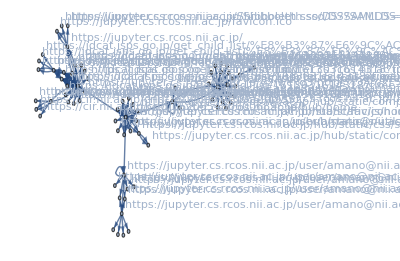
{20230724-20230725-ipaddr,{1,1},-Graphics-}

```mathematica
storyGrIdxFlDs[3][[2]]
```

4. 不要と思われるvertexを削除(1)：

```mathematica
(storyGrIdxFlDsVD1[3]=Map[{#[[1]],#[[2]],If[VertexQ[#[[3]],"-"],VertexDelete[#[[3]],"-"],#[[3]]]}&,storyGrIdxFlDs[3]])//Dimensions
```

{17,3}

5. 不要と思われるvertexを削除(2)：

rm候補のパターン：

```mathematica
rmpattAll[4]={rmpatt[4][1]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/static.*"],
rmpatt[4][2]=RegularExpression["https://jdcat.jsps.go.jp/api.*"],
rmpatt[4][3]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*"],
rmpatt[4][4]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*"],
rmpatt[4][5]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/img.*"],
rmpatt[4][6]=RegularExpression["https://.*/.*\\.svg"],
rmpatt[4][7]=RegularExpression["https://.*/.*\\.js"],
rmpatt[4][8]=RegularExpression["https://jupyter.cs.rcos.nii.ac.jp/.*\\.js\\?.*"],
rmpatt[4][9]=RegularExpression["https://jdcat.jsps.go.jp/.*\\.js\\?.*"],
rmpatt[4][10]=RegularExpression["https://.*/.*\\.woff2.*"],
rmpatt[4][11]=RegularExpression["https://.*/.*\\.css"],
rmpatt[4][12]=RegularExpression["https://.*/css/.*"],
rmpatt[4][13]=RegularExpression["https://.*/.*\\.favicon.ico"],
rmpatt[4][14]="https://jdcat.jsps.go.jp/get_search_setting",
rmpatt[4][15]="https://jdcat.jsps.go.jp/facet-search/get-title-and-order"
}
```

{RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/static.*],RegularExpression[https://jdcat.jsps.go.jp/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/hub/.*api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/user/.*/api.*],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/img.*],RegularExpression[https://.*/.*\.svg],RegularExpression[https://.*/.*\.js],RegularExpression[https://jupyter.cs.rcos.nii.ac.jp/.*\.js\?.*],RegularExpression[https://jdcat.jsps.go.jp/.*\.js\?.*],RegularExpression[https://.*/.*\.woff2.*],RegularExpression[https://.*/.*\.css],RegularExpression[https://.*/css/.*],RegularExpression[https://.*/.*\.favicon.ico],https://jdcat.jsps.go.jp/get_search_setting,https://jdcat.jsps.go.jp/facet-search/get-title-and-order}

rm候補のパターンから削除頂点リストを生成（参考）：

```mathematica
createRmList[gr_,rmpatt_]:=Module[{vlist},
vlist=VertexList[gr];
Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]]
]
```

rm候補のパターンを指定してグラフからマッチする頂点を削除する関数：

```mathematica
rmV[gr_,rmpatt_]:=Module[{vlist,pathlist},
vlist=VertexList[gr];
pathlist=Union[Flatten[Table[Cases[vlist,x_/;StringMatchQ[x,rmpatt[[n]]]],{n,Length[rmpatt]}]]];
VertexDelete[gr,pathlist]
]
```

```mathematica
(storyGrIdxFlDsVD2[3]=Map[{#[[1]],#[[2]],rmV[#[[3]],rmpattAll[4]]}&,storyGrIdxFlDsVD1[3]])//Dimensions
```

{17,3}

6. 以上の操作により不正となったグラフを削除(対象をpick)：

ノード数 >= 2：

```mathematica
pickPos[3][1]=Flatten[Position[Map[VertexCount[#[[3]]]&,storyGrIdxFlDsVD2[3]],x_/;x>=2]];
```

```mathematica
(storyGrIdxFlDs2[3]=storyGrIdxFlDsVD2[3][[pickPos[3][1]]])//Dimensions
```

{14,3}

エッジ数 >= 1：

```mathematica
pickPos[3][2]=Flatten[Position[Map[EdgeCount[#[[3]]]&,storyGrIdxFlDs2[3]],x_/;x>=1]];
```

```mathematica
(storyGrIdxFlDs3[3]=storyGrIdxFlDs2[3][[pickPos[3][2]]])//Dimensions
```

{14,3}

上が分離されたストーリー

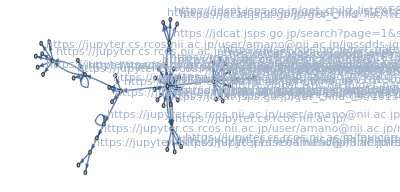
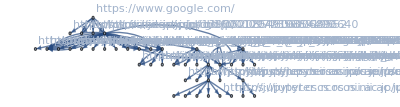
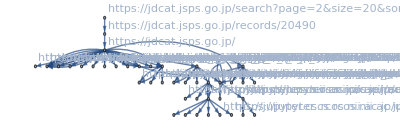
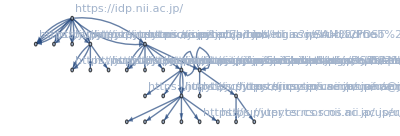
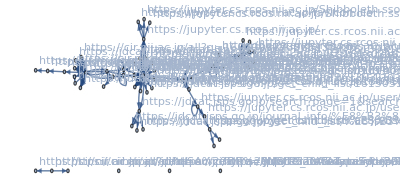
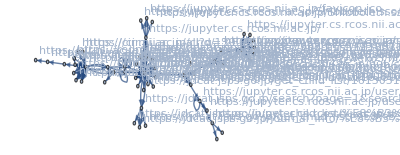
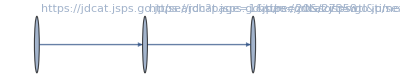
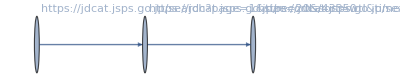
{{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-},{20230724-20230725-ipaddr,{1,1},-Graphics-}}

```mathematica
storyGrIdxFlDs3[3]
```

#### Pre Op 2.2.1 : save

```mathematica
savedir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=4/_story

```mathematica
SetDirectory[savedir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=4/_story

```mathematica
Directory[]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=4/_story

```mathematica
(*Timing[Save["storyGrIdxFlDs3.save",storyGrIdxFlDs3]]
Timing[Save["storyGrIdxFlDs3.save",toCRID]]
Timing[Save["ckan.save",ckanName]]
Timing[Save["ckan.save",ckanCridAC]]
Timing[Save["ckan.save",ckanCridPLogPosAC]]
Timing[Save["ckan.save",ckanCridRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRLogPosAC]]
Timing[Save["ckan.save",ckanCridPRACQ]]*)
```

<<< Saveデータを読んだ時はここまで飛ばす。 >>>

## Analysis

#### Analysis 1

基本属性

エッジ:

```mathematica
(eltbl[3]=Table[EdgeList[storyGrIdxFlDs3[3][[i]][[3]]],{i,Length[storyGrIdxFlDs3[3]]}])//Dimensions
```

{14}

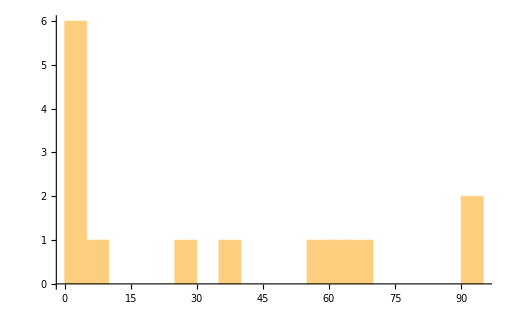

```mathematica
Histogram[Map[Length,eltbl[3]],{5}]
```

ノード:

```mathematica
(vltbl[3]=Table[VertexList[storyGrIdxFlDs3[3][[i]][[3]]],{i,Length[storyGrIdxFlDs3[3]]}])//Dimensions
```

{14}

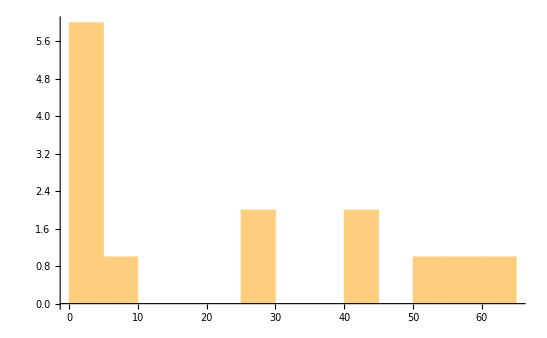

```mathematica
Histogram[Map[Length,vltbl[3]],{5}]
```

アクセス時刻:

```mathematica
(acct[3]=Map[#[[3,1]]&,eltbl[3],{2}])//Dimensions
```

{14}

滞留時間：

```mathematica
(accspanMin[3]=Map[Max[#]-Min[#]&,acct[3]]/60)//Dimensions
```

{14}

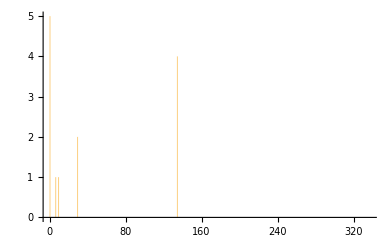

```mathematica
Histogram[accspanMin[3],{1}]
```

スタートノードが最小時刻になっていない。調整が必要か？

E/V ratio:

```mathematica
(ratioEV[3]=Map[Length,eltbl[3]]/Map[Length,vltbl[3]]//N)//Dimensions
```

{14}

TV ratio :

```mathematica
(ratioTV[3]=acct[3]/Map[Length,vltbl[3]])//Dimensions
```

{14}

TE ratio:

```mathematica
(ratioTE[3]=acct[3]/Map[Length,eltbl[3]])//Dimensions
```

{14}

#### Analysis 2

リクエストパスから基盤名だけをとりだし、基盤連携を見る。

```mathematica
(GrBases[3]=Map[fqdnFromGraph[#[[3]]]&,storyGrIdxFlDs3[3]])//Dimensions
```

{14}

```mathematica
GrBases[3]//TableForm
```

https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:cir.nii.ac.jp | https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp | https:www.google.com
https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:idp.nii.ac.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:cir.nii.ac.jp | https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp | 
https:cir.nii.ac.jp | https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp | https:redmine.devops.rcos.nii.ac.jp
https:jdcat.jsps.go.jp |  |  | 
https:jdcat.jsps.go.jp |  |  | 
https:jdcat.jsps.go.jp |  |  | 
https:jdcat.jsps.go.jp |  |  | 
https:jupyter.cs.rcos.nii.ac.jp |  |  | 
https:binder.cs.rcos.nii.ac.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:binder.cs.rcos.nii.ac.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:binder.cs.rcos.nii.ac.jp | https:jupyter.cs.rcos.nii.ac.jp |  |

NII基盤(4基盤以外も)へのアクセスを見る。

```mathematica
niidnpos=Flatten[Position[Map[StringMatchQ[#,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[#,RegularExpression[".*jdcat.jsps.go.jp.*"]]&,Flatten[GrBases[3]]//Union],True]]
```

{1,2,3,4,5,6}

```mathematica
(Flatten[GrBases[3]]//Union)[[niidnpos]]
```

{https:binder.cs.rcos.nii.ac.jp,https:cir.nii.ac.jp,https:idp.nii.ac.jp,https:jdcat.jsps.go.jp,https:jupyter.cs.rcos.nii.ac.jp,https:redmine.devops.rcos.nii.ac.jp}

```mathematica
(GrNiiBases[3]=Map[Cases[#,x_/;StringMatchQ[x,RegularExpression[".*nii.ac.jp.*"]]||StringMatchQ[x,RegularExpression[".*jdcat.jsps.go.jp.*"]]]&,GrBases[3]])//Dimensions
```

{14}

```mathematica
GrNiiBases[3]//TableForm
```

https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:cir.nii.ac.jp | https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp | 
https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:idp.nii.ac.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:cir.nii.ac.jp | https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp | 
https:cir.nii.ac.jp | https:jdcat.jsps.go.jp | https:jupyter.cs.rcos.nii.ac.jp | https:redmine.devops.rcos.nii.ac.jp
https:jdcat.jsps.go.jp |  |  | 
https:jdcat.jsps.go.jp |  |  | 
https:jdcat.jsps.go.jp |  |  | 
https:jdcat.jsps.go.jp |  |  | 
https:jupyter.cs.rcos.nii.ac.jp |  |  | 
https:binder.cs.rcos.nii.ac.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:binder.cs.rcos.nii.ac.jp | https:jupyter.cs.rcos.nii.ac.jp |  | 
https:binder.cs.rcos.nii.ac.jp | https:jupyter.cs.rcos.nii.ac.jp |  |

```mathematica
Map[Length,GrBases[3]]//Tally
```

{{2,6},{4,2},{3,1},{1,5}}

```mathematica
(GrBasesTly[3]=Tally[GrBases[3]])//Dimensions
```

{8,2}

```mathematica
Map[Length,GrNiiBases[3]]//Tally
```

{{2,6},{3,2},{4,1},{1,5}}

```mathematica
(GrNiiBasesTly[3]=Tally[GrNiiBases[3]])//Dimensions
```

{7,2}

```mathematica
GrNiiBasesTly[3]//TableForm
```

https:jdcat.jsps.go.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp
https:jupyter.cs.rcos.nii.ac.jp | 2
https:idp.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 1
https:cir.nii.ac.jp
https:jdcat.jsps.go.jp
https:jupyter.cs.rcos.nii.ac.jp
https:redmine.devops.rcos.nii.ac.jp | 1
https:jdcat.jsps.go.jp | 4
https:jupyter.cs.rcos.nii.ac.jp | 1
https:binder.cs.rcos.nii.ac.jp
https:jupyter.cs.rcos.nii.ac.jp | 3

グラフが多すぎるので選び方を考え中。

ここから、Idpで認証されたログはIdpがリファラーとして入ってくるが、認証元情報がはいらないため基盤連携のグラフに組み込まれない。
 一方で、Idpを遮蔽して認証元からアクセス先へのエッジは発生する。

#### Analysis 3 CKAN impact

ckanCRIDを含むグラフを抽出する。

すでに構成したハッシュとグラフのプロパティを当てる関数。ひとつでもあたればTrueを返す。
 ハッシュはログ中の位置を記述しており、リクエストパス・リファラーを分けたもの、Unionしたもの。

滞留時間をグラフから得る関数：

```mathematica
stayTime[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Map[#[[3,1]]&,elist];
Max[tlist]-Min[tlist]
]
```

ckanCRIDを含むログの行とグラフのエッジにあるログの行を当てる関数 （T/F）:

```mathematica
logGraphQ[gr_Graph,asc_Association]:=Module[{elist,logposlist,res},
elist=EdgeList[gr];
logposlist=Map[#[[3,2]]&,elist];
res=Map[asc[#]&,logposlist];
Position[res,_Integer,{1}]/.{{}->False,{__}->True}
]
```

ckanCRIDをリクエストに含むノードをハイライトする関数：

```mathematica
ckanVertexHighlihgt[g_Graph,asc_Association]:=Module[{vlist,pos,targetv,op},
vlist=VertexList[g];
pos=Flatten[Position[Map[ckanCridPRACQ[toCRID[#]]&,VertexList[g]],True]];
targetv=vlist[[pos]];
op=VertexStyle->Map[#->Red&,targetv];
Graph[g,op]
]
```

CKAN - CRIDを含むグラフの抽出

```mathematica
(ckanGrP[3]=Map[If[logGraphQ[#[[3]],ckanCridPLogPosAC[3]],#,Null]&,storyGrIdxFlDs3[3]])//Dimensions
```

{14}

```mathematica
ckanGrP[4][[2]]
```

Part::partw: Part 2 of ckanGrP[4] does not exist.

ckanGrP[4]⟦2⟧

```mathematica
(ckanGrR[3]=Map[If[logGraphQ[#[[3]],ckanCridRLogPosAC[3]],#,Null]&,storyGrIdxFlDs3[3]])//Dimensions
```

{14}

```mathematica
(ckanGrPR[3]=Map[If[logGraphQ[#[[3]],ckanCridPRLogPosAC[3]],#,Null]&,storyGrIdxFlDs3[3]])//Dimensions
```

{14}

```mathematica
(ckanGrPsel[3]=Cases[ckanGrP[3],{__},{1}])//Dimensions
```

{0}

```mathematica
ckanGrPselVL[3]=Map[VertexList[#[[3]]]&,ckanGrPsel[3]];
```

```mathematica
ckanGrPselEL[3]=Map[EdgeList[#[[3]]]&,ckanGrPsel[3]];
```

```mathematica
(ckanGrRsel[3]=Cases[ckanGrR[3],{__},{1}])//Dimensions
```

{0}

```mathematica
ckanGrRselVL[3]=Map[VertexList[#[[3]]]&,ckanGrRsel[3]];
```

```mathematica
ckanGrRselEL[3]=Map[EdgeList[#[[3]]]&,ckanGrRsel[3]];
```

```mathematica
(ckanGrPRsel[3]=Cases[ckanGrPR[3],{__},{1}])//Dimensions
```

{0}

```mathematica
ckanGrPRselVL[3]=Map[VertexList[#[[3]]]&,ckanGrPRsel[3]];
```

```mathematica
ckanGrPRselEL[3]=Map[EdgeList[#[[3]]]&,ckanGrPRsel[3]];
```

```mathematica
(ckanGrPRselHL[3]=Map[{#[[1]],#[[2]],ckanVertexHighlihgt[#[[3]],ckanCridPRACQ]}&,ckanGrPRsel[3]])//Dimensions
```

{0}

```mathematica
ckanGrPRVcount[3]=Map[VertexCount[#[[3]]]&,ckanGrPRselHL[3]]
```

{}

```mathematica
accTimeList[g_Graph]:=Module[{elist,tlist},
elist=EdgeList[g];
tlist=Sort[Map[#[[3,1]]&,elist],#1>#2&]
]
```

```mathematica
timeSpan[tlist_]:=Map[(#[[1]]-#[[2]])&,Partition[tlist,2,1]]
```

```mathematica
ckanGrPRstayTime[3]=Map[stayTime[#[[3]]]&,ckanGrPRselHL[3]]
```

{}

#### Analysis 4 CKAN graph reform

program :

可能な全Vertexにアクセス時間リストを付与：

```mathematica
gatherDistributeUniq[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
{first,target}
]
```

```mathematica
gatherDistributeUniqRl[l_]:=Module[{first,target},
first=l[[1,1]];
target=Map[#[[2]]&,l];
first->{first,target}
]
```

```mathematica
addVertexAccTime[g_]:=Module[{gatherTimeV,gatherTimeVRl},
gatherTimeV=Gather[Map[{#[[2]],#[[3,1]]}&,EdgeList[g]],#1[[1]]==#2[[1]]&];
gatherTimeVRl=Map[gatherDistributeUniqRl,gatherTimeV];
VertexReplace[g,gatherTimeVRl]
]
```

```mathematica
guessVertexCoorGr[g_,timeshift_]:=Module[{allAccTime,baseTime,repPos,target,repRl},
allAccTime=Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real];
baseTime=Min[allAccTime]+timeshift;
repPos=Flatten[Position[Map[Head,VertexList[g]],String]];
target=Map[VertexList[g][[#]]&,repPos];
repRl=Map[#->{#,{baseTime}}&,target];
VertexReplace[g,repRl]
]
```

```mathematica
accTimeMinGr[g_]:=Min[Cases[Flatten[Map[#[[2]]&,g//VertexList]],_Real]]
```

```mathematica
reformCoorGr[g_,baseTime_,f_]:=f[Map[{Max[#[[2]]],Min[#[[2]]]}&,VertexList[g]]-baseTime]
```

```mathematica
timeLineGr[g_,timeshift_,f_]:=Module[{gnew,btime,coornew},
gnew=guessVertexCoorGr[g,timeshift];
btime=accTimeMinGr[gnew];
coornew=reformCoorGr[gnew,btime,Sqrt];
Graph[gnew,VertexSize->Automatic,VertexCoordinates->coornew]
]
```

```mathematica
(ckanGrPRselHLAT[3]=Map[{#[[1]],#[[2]],addVertexAccTime[#[[3]]]}&,ckanGrPRselHL[3]])//Dimensions
```

{0}

ロググループ：

```mathematica
loggroupCKAN=Map[#[[2]]&,ckanGrPRselHLAT[3]]
```

{}

ノードの数え上げ：

```mathematica
vcCKAN=Map[VertexCount[#[[3]]]&,ckanGrPRselHLAT[3]]
```

{}

エッジの数え上げ：

```mathematica
ecCKAN=Map[EdgeCount[#[[3]]]&,ckanGrPRselHLAT[3]]
```

{}

アクセス時刻：

```mathematica
(accCKAN=Map[Map[#[[3,1]]&,EdgeList[#[[3]]]]&,ckanGrPRselHLAT[3]])//Dimensions
```

{0}

最大滞在時間：

```mathematica
maxTimeSpan[l_]:=Max[Map[#[[1]]-#[[2]]&,Partition[Sort[l,#1>#2&],2,1]]]
```

```mathematica
(maxtimespanCKAN=Map[maxTimeSpan,accCKAN]/.{-Infinity->0})/60
```

{}

滞留時間：

```mathematica
staytimeCKAN=Map[Max[#]-Min[#]&,accCKAN]
```

{}

```mathematica
staytimeCKAN/60
```

{}

```mathematica
f[x_]=Log[x+1]
```

Log[1+x]

```mathematica
(ckanGrPRselHLTL[3]=Map[timeLineGr[#[[3]],-60,f]&,ckanGrPRselHLAT[3]])//Dimensions
```

{0}

```mathematica
ckanGrPRselHLTL[3]//TableForm
```

{}

#### Report:CKAN impact

```mathematica
logtbl={{"- ログ件数 -","述べログ件数"},{{"全件数","ユーザーアクセス件数"},{ToExpression[StringSplit[logwc][[1]]],idxLog[3]//Length}}}//TableForm
```

- ログ件数 - | 述べログ件数
全件数
ユーザーアクセス件数 | 1205
259

```mathematica
ckanlogtbl={{"- CKAN-cridを含むログ件数 -","述べログ件数","cridのユニーク件数"},{{"リクエストにCKAN-crid含む","リファラーにCKAN-crid含む","いずれか含む"},{ckanCridPLogPos[3]//Length,ckanCridRLogPos[3]//Length,ckanCridPRLogPos[3]//Length},{Union[ckanCridPlist]//Length,Union[ckanCridRlist]//Length,ckanCridPRU//Length}}}//TableForm
```

- CKAN-cridを含むログ件数 - | 述べログ件数 | cridのユニーク件数
リクエストにCKAN-crid含む
リファラーにCKAN-crid含む
いずれか含む | 0
0
0 | 0
0
0

```mathematica
ckanchaintbl={{"- アクション連鎖数 -","件数"},{{"全件数","ノードにCKAN-crid含む"},{storyGrIdxFlDs3[3]//Length,ckanGrPRselHL[3]//Length}}}//TableForm
```

- アクション連鎖数 - | 件数
全件数
ノードにCKAN-crid含む | 14
0

```mathematica
ckangrsummarytbl={{"アクセスグラフ通し番号","ロググループ","ノード数","エッジ数","最大滞在時間(分)","滞留時間(分)"},{Table[i,{i,Length[loggroupCKAN]}],loggroupCKAN,vcCKAN,ecCKAN,maxtimespanCKAN/60,staytimeCKAN/60}}//TableForm
```

アクセスグラフ通し番号 | ロググループ | ノード数 | エッジ数 | 最大滞在時間(分) | 滞留時間(分)
 |  |  |  |  |

### Export:CKAN impact

エクスポート用：

```mathematica
(ckanEL=Map[MapApply[List,EdgeList[#]]&,ckanGrPRselHLTL[3]])//Dimensions
```

{0}

```mathematica
(ckanELX=Map[{#[[1,1]],#[[2,1]]}&,ckanEL,{2}])//Dimensions
```

{0}

```mathematica
expdir=mountdir<>"log/D="<>date<>"/T=4/_story"
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=4/_story

```mathematica
SetDirectory[expdir]
```

/Volumes/IODATA/NII/togo-log/rcoslogs/log/D=20230724-20230725-ipaddr/T=4/_story

```mathematica
(*Export["ckanedgelist.json",ckanELX]*)
```

## 終端処理

```mathematica
end=AbsoluteTime[Date[]]
```

3.908880715180716×10^9

```mathematica
end-start
```

14.15596